```mathematica
FindContractedFormulae[g_]:=Block[{edges,full,implied={}},
edges=EdgeList[GraphComplement[g]];
Monitor[
Table[With[{
contract =Graph[VertexContract[g,{e[[1]],e[[2]]}],VertexLabels->"Name",GraphHighlight->{e[[1]]},GraphHighlightStyle->"Thick",GraphLayout->"TutteEmbedding", ImageSize->40]
},
Map[SymbolReplace[#,e]&,FindFullFormula[contract]]
],{e,Sort[Map[SortEdge,edges]]}],
e]
]
```

```mathematica
Finest[forms_]:=Block[{result,level=0,current},
Table[
current=SymbolLevel[f];
If[current>level,result=f;level=current]
,{f,forms}
];
result
]
```

```mathematica
Finest [{v1x2x35x4x6,v1x2x35x46}]
```

v1x2x35x4x6

```mathematica
Map [SymbolLevel,{v1x2x35x4x6,v1x2x35x46}]
```

{5,4}

```mathematica
FindFiner[SymbolToSets[v1x2x35x4x6]]
```

{{{1},{2},{3},{4},{5},{6}}}

```mathematica
Map[{Finest[#],#}&,FindContractedFormulae[MinimalGraph[5]]]
```

{{v1x2x35x4x6,{v1x2x35x4x6,v1x2x35x46}},{v1x2x36x4x5,{v1x2x36x4x5}},{v1x2x3x46x5,{v1x2x3x46x5,v1x2x35x46}}}

```mathematica
With [{form=DeleteDuplicates[Flatten[FindContractedFormulae[MinimalGraph[5]]]]},
FindFiner[SymbolToSets[Finest[form]]]
]
```

{{{1},{2},{3},{4},{5},{6}}}

```mathematica
SetsToSymbol2[{{1},{2},{3},{4},{5},{6}}]
```

v1x2x3x4x5x6

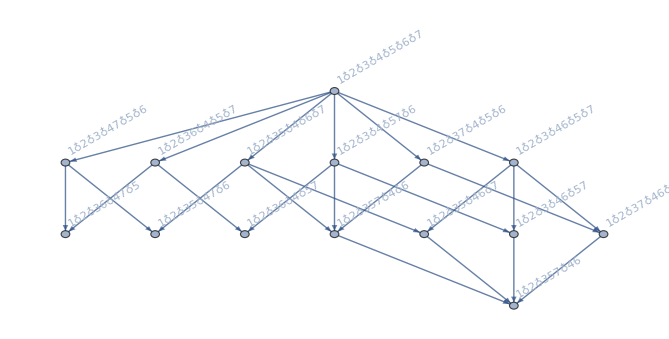

```mathematica
With [{form=DeleteDuplicates[Flatten[FindContractedFormulae[MinimalGraph[6]]]]},
Prepend[form,SetsToSymbol[First[FindFiner[SymbolToSets[Finest[form]]]]]]//FormulaGraphReverse2
]
```

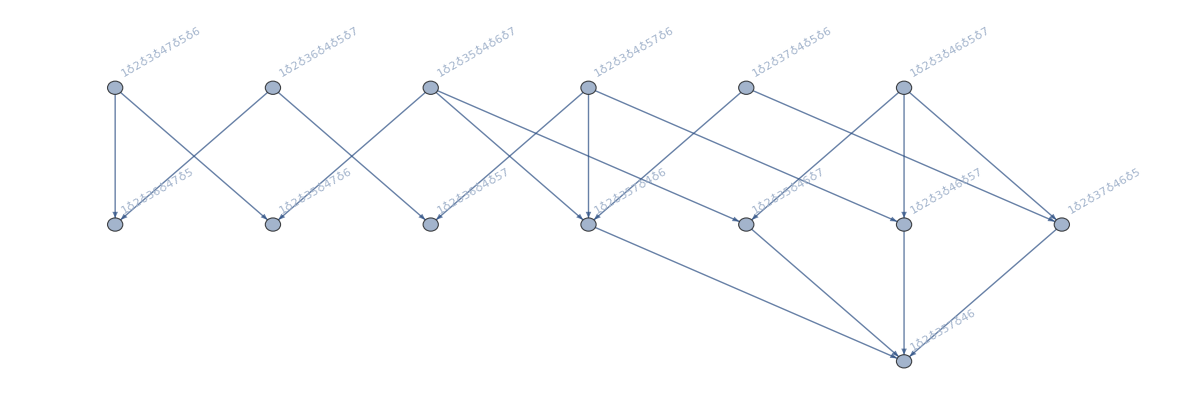

```mathematica
FindContractedFormulae[MinimalGraph[6]]//Flatten//DeleteDuplicates//FormulaGraphReverse2
```

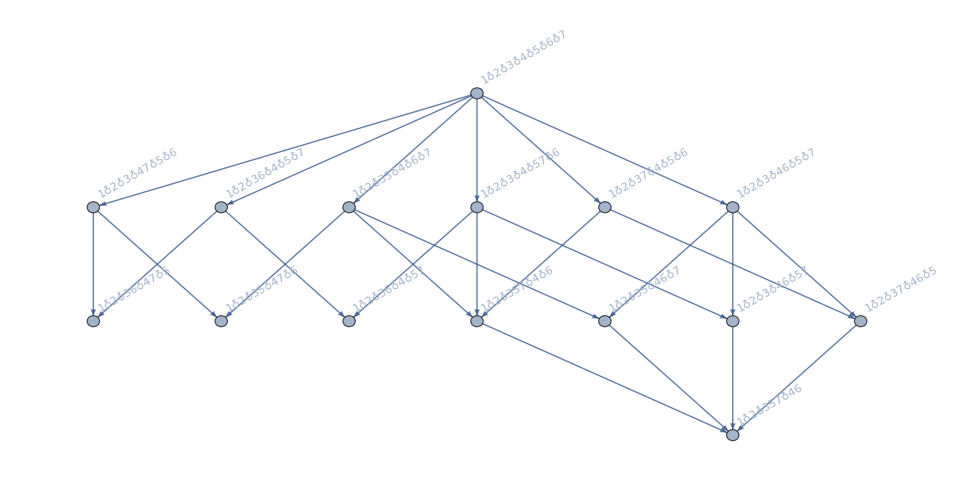

```mathematica
FindFullFormula[MinimalGraph[6]]//Flatten//DeleteDuplicates//FormulaGraphReverse2
```

```mathematica
FindContractedFormulae2[g_]:=Block[{edges,full,implied={}},
edges=EdgeList[g];
Monitor[
Table[With[{
contract =Graph[VertexContract[g,{e[[1]],e[[2]]}],VertexLabels->"Name",GraphHighlight->{e[[1]]},GraphHighlightStyle->"Thick",GraphLayout->"TutteEmbedding", ImageSize->40]
},
Map[SymbolReplace[#,e]&,FindFullFormula[contract]]
],{e,Sort[Map[SortEdge,edges]]}],
e]
]
```

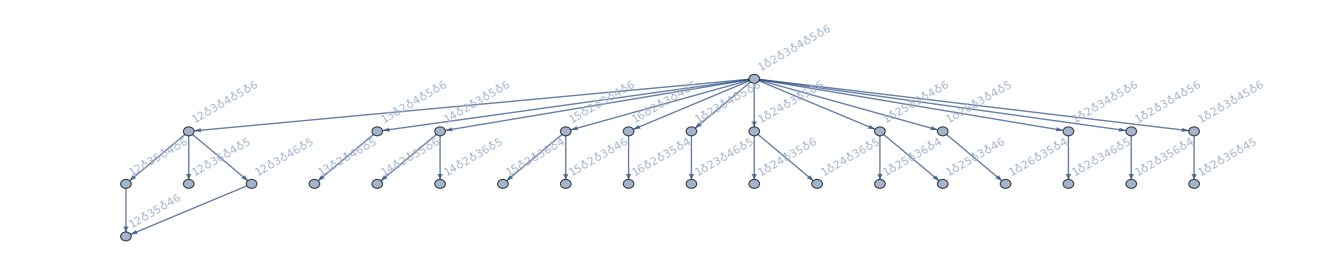

```mathematica
With [{form=DeleteDuplicates[Flatten[FindContractedFormulae2[MinimalGraph[5]]]]},
Prepend[form,SetsToSymbol[First[FindFiner[SymbolToSets[Finest[form]]]]]]//FormulaGraphReverse2
]
```

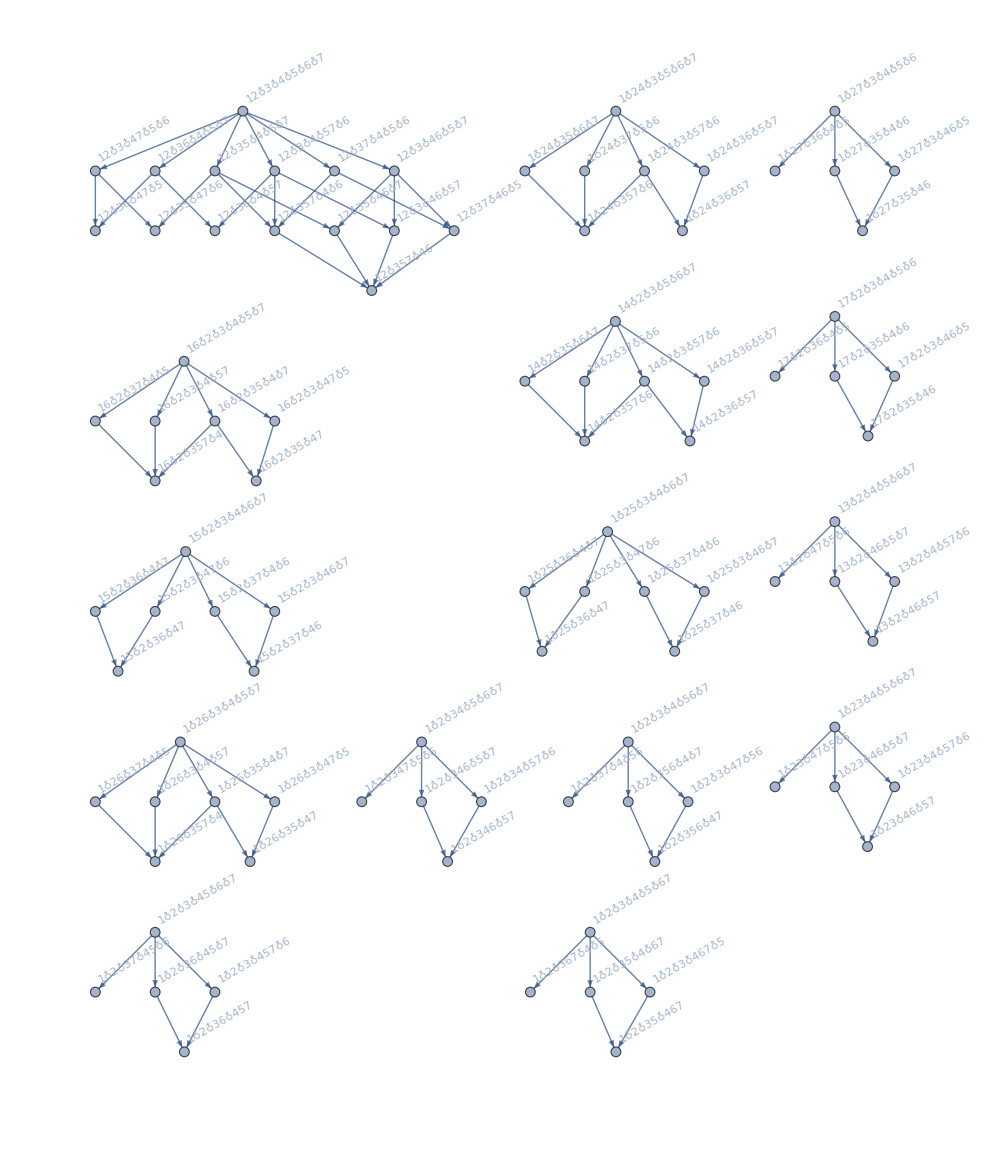

```mathematica
FindContractedFormulae2[MinimalGraph[6]]//Flatten//DeleteDuplicates//FormulaGraphReverse2
```